# 指定された地域間の移動者数の可視化

## 阿川真士 2020.6.25 改訂：溝口佳寛 2020/07/15 更に改訂：阿川真士 2020.7.23

Ryo2Package.wl をデスクトップに置きます.

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Desktop/"}]];
<<Ryo2Package`;
```

## 1. 実行例

#### 1.1.1 札幌、東京、大阪、福岡、那覇の移動者数の表示。

array1に移動者数の行列が保存され、label3に都市名が保存されている。

```mathematica
?array1
```

```mathematica
?label3
```

label3[[5]] が札幌、label3[[17]] が東京、label3[[31]] が大阪、label3[[44]] が福岡、lanel3[[51]] が那覇を表している。

```mathematica
label3[[{5,17,31,44,51}]]
```

{{5.,札幌},{17.,東京},{31.,大阪},{44.,福岡},{51.,那覇}}

指定した都市間のデータのみを抽出し、表の形で表示する。

```mathematica
CityTable[array1,label3,{5,17,31,44,51}]
```

| 札幌 | 東京 | 大阪 | 福岡 | 那覇
札幌 | 788638. | 6617.75 | 1258.45 | 283.285 | 50.708
東京 | 6609.42 | 9.66483×10^6 | 14083.5 | 5309.85 | 3296.66
大阪 | 1259.73 | 14129.8 | 2.94672×10^6 | 3081.45 | 1309.15
福岡 | 290.785 | 5256.35 | 3107.11 | 817121. | 985.687
那覇 | 51.049 | 3289.42 | 1316.22 | 987.354 | 107268.

指定した都市間のデータのみを抽出し、辺上に移動者数を記したグラフで可視化する。

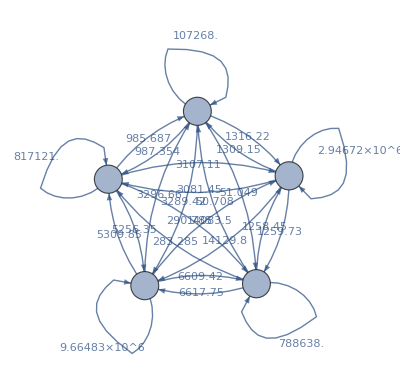

```mathematica
CityGraph[array1,label3,{5,17,31,44,51}]
```

#### 1.1.2 グラフの頂点を地図上に配置する準備。

福岡、佐賀、長崎を色と太さを変えて結ぶ。

```mathematica
TrianglizationConnecter["Fukuoka", "Saga", "Nagasaki"]
```

-Graphics-

#### 1.1.3 ３都市を地図上に配置し移動者数を色と太さで可視化する。

```mathematica
?ThreePointsView
```

福岡、長崎、熊本間の移動者数をグラフの頂点を地図上に配置し色と太さで可視化。

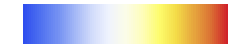
-Graphics- -Graphics-

```mathematica
ThreePointsView[array1,label3,{44,46,47}]
```

#### 1.1.4 ４都市を地図上に配置し移動者数を色と太さで可視化する。

```mathematica
?FourPointsView
```

青森、秋田、宮城、岩手間の移動者数をグラフの頂点を地図上に配置し色と太さで可視化。

```mathematica
FourPointsView[array1,label3,{6,7,8,9}]
```

-Graphics- -Graphics-

## 2. 今後の予定

(1)ラベルを県庁所在地に書き換える必要がある。
(2)都市名を番号で入れないようにする。
(3)４都市以上の可視化。
(4)線の太さや色の変化の調整。
(5)デモファイルの充実化。